```mathematica
SetDirectory[NotebookDirectory[]];
```

#### No ip correlations

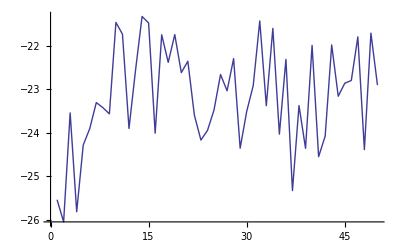

-23.173

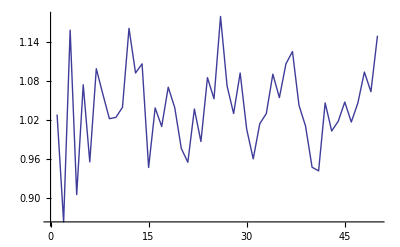

1.03921

```mathematica
data=Import["noipcorr.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```

#### ip correlations

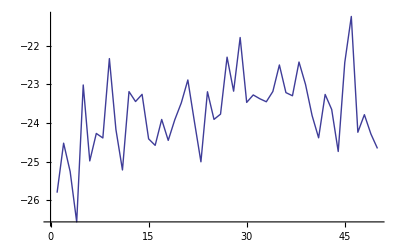

-23.7327

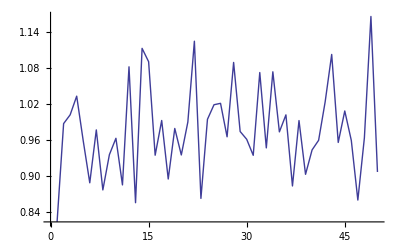

0.97651

```mathematica
data=Import["ipcorr.dat"];
En=Transpose[data][[4]];
errEn=Transpose[data][[6]];
ListPlot[En,Joined->True]
Mean[En]
ListPlot[errEn,Joined->True]
Mean[errEn]
```